```mathematica
With[{subFigureA=Labeled[GraphicsRow[Map[ArrayPlot[CellularAutomaton[{{0,2,_}->5,{5,3,_}->5,{5,_,_}->1,{_,5,_}->1,{_,2,_}->3,{_,3,2}->2,{_,1,2}->4,{_,4,_}->3,{4,3,_}->4,{4,0,_}->2,{_,x_,_}->x},{Join[Table[1,#1],{2}],0},{{0,80},{-5,8+2*(#1-1)}}],ColorRules-><|0->White,1->Black,5->GrayLevel[0.8],_->Gray|>,Mesh->True,MeshStyle->Black]&,Range[5]]],Text[Style["(a)",Italic]]],subFigureB=Labeled[GraphicsRow[Map[ArrayPlot[CellularAutomaton[<|"RuleNumber"->5407067979,"Colors"->3|>,{Join[Table[1,#1-1],{2}],0},{{0,36},{-4,5+2*(#1-1)}}],ColorRules-><|0->White,1->Black,2->GrayLevel[0.5]|>,Mesh->True,MeshStyle->Black]&,Range[7]]],Text[Style["(c)",Italic]]],subFigureC=Labeled[GraphicsRow[Map[ArrayPlot[CellularAutomaton[{{_,2,_}->3,{_,1,2}->2,{3,0,_}->1,{3,_,_}->3,{_,3,_}->1,{_,x_,_}->x},{Join[Table[1,#1-1],{2}],0},{{0,36},{-4,5+2*(#1-1)}}],ColorRules-><|0->White,1->Black,3->GrayLevel[0.8],_->Gray|>,Mesh->True,MeshStyle->Black]&,Range[7]]],Text[Style["(b)",Italic]]]},Grid[{{subFigureA,Column[{subFigureB,subFigureC}]}},Alignment->{Center,Bottom}]]
```

```mathematica
subFigureC=Labeled[GraphicsRow[Map[ArrayPlot[CellularAutomaton[{{_,2,_}->3,{_,1,2}->2,{3,0,_}->1,{3,_,_}->3,{_,3,_}->1,{_,x_,_}->x},{Join[Table[1,#1-1],{2}],0},{{0,36},{-4,5+2*(#1-1)}}],ColorRules-><|0->White,1->Black,3->GrayLevel[0.8],_->Gray|>,Mesh->True,MeshStyle->Black]&,Range[7]]],Text[Style["(b)",Italic]]]
```

-Graphics-(b)

```mathematica
subFigureC=Labeled[GraphicsRow[Map[ArrayPlot[CellularAutomaton[{340282028880983993981473709559457473792, 4, 1},{Join[Table[1,#1-1],{2}],0},{{0,36},{-4,5+2*(#1-1)}}],ColorRules-><|0->White,1->Black,3->GrayLevel[0.8],_->Gray|>,Mesh->True,MeshStyle->Black]&,Range[7]]],Text[Style["(b)",Italic]]]
```

-Graphics-(b)

```mathematica
{{"[◼]", "CustomStyleData"}}["Colors"]
```

{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]}

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},110],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.1]],RulePlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

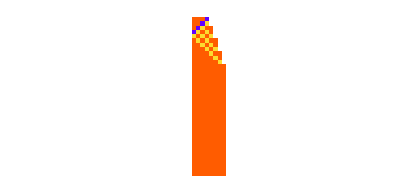

```mathematica
ArrayPlot[CellularAutomaton[{{_,2,_}->3,{_,1,2}->2,{3,0,_}->1,{3,_,_}->3,{_,3,_}->1,{_,x_,_}->x}, {Append[Table[1, 3], 2], 0}, {36, All}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]
```

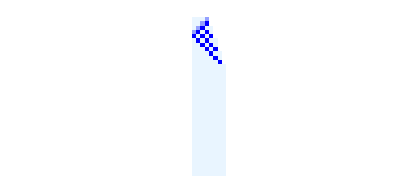

```mathematica
ArrayPlot[CellularAutomaton[{{_,2,_}->3,{_,1,2}->2,{3,0,_}->1,{3,_,_}->3,{_,3,_}->1,{_,x_,_}->x}, {Append[Table[1, 3], 2], 0}, {36, All}], ColorFunction->(Blend[{White, LightBlue, Blue}, #]& )]
```

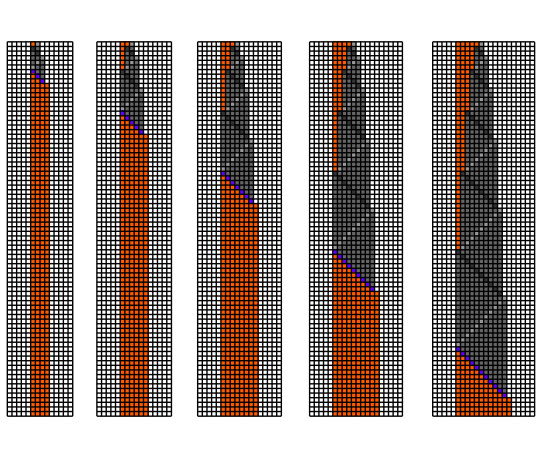
-Graphics-(a)

```mathematica
subFigureA=Labeled[GraphicsRow[Map[ArrayPlot[CellularAutomaton[{{0,2,_}->5,{5,3,_}->5,{5,_,_}->1,{_,5,_}->1,{_,2,_}->3,{_,3,2}->2,{_,1,2}->4,{_,4,_}->3,{4,3,_}->4,{4,0,_}->2,{_,x_,_}->x},{Join[Table[1,#1],{2}],0},{{0,80},{-5,8+2*(#1-1)}}],ColorRules-><|0->White,1->Hue[0.06, 1, 1],5->Hue[0.73, 1, 1]|>,Mesh->True,MeshStyle->Black]&,Range[5]]],Text[Style["(a)",Italic]]]
```

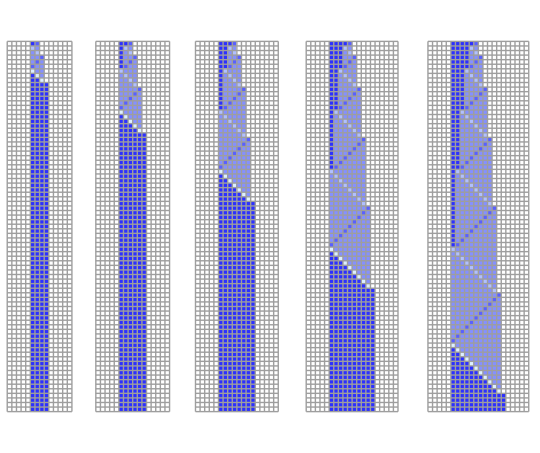
-Graphics-(a)

```mathematica
subFigureA=Labeled[GraphicsRow[Map[ArrayPlot[CellularAutomaton[{{0,2,_}->5,{5,3,_}->5,{5,_,_}->1,{_,5,_}->1,{_,2,_}->3,{_,3,2}->2,{_,1,2}->4,{_,4,_}->3,{4,3,_}->4,{4,0,_}->2,{_,x_,_}->x},{Join[Table[1,#1],{2}],0},{{0,80},{-5,8+2*(#1-1)}}],ColorFunction->(If[# ==0, White, Blend[{Blue, LightBlue}, #]]& ),Mesh->True]&,Range[5]]],Text[Style["(a)",Italic]]]
```

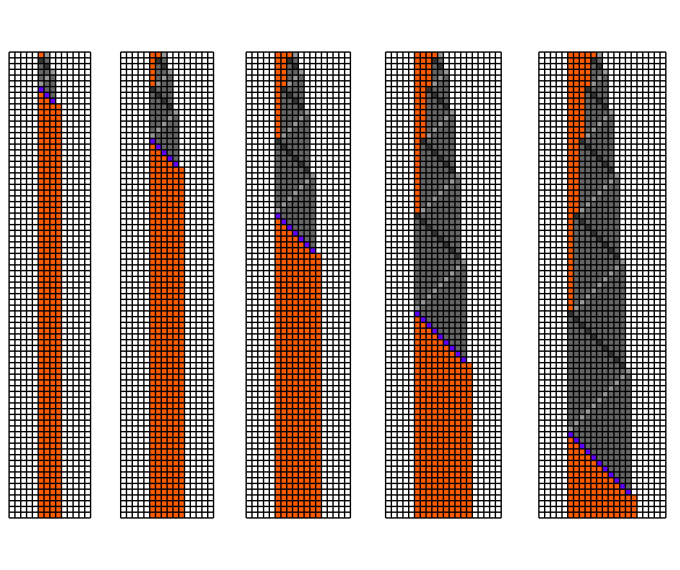
-Graphics-(a)

```mathematica
subFigureA=Labeled[GraphicsRow[Map[ArrayPlot[CellularAutomaton[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,#1],{2}],0},{{0,80},{-5,8+2*(#1-1)}}],ColorRules-><|0->White,1->Hue[0.06, 1, 1],5->Hue[0.73, 1, 1]|>,Mesh->True,MeshStyle->Black]&,Range[5]]],Text[Style["(a)",Italic]]]
```

```mathematica
8+2*(3-1)
```

12

```mathematica
RulePlot[CellularAutomaton[{{0,2,_}->5,{5,3,_}->5,{5,_,_}->1,{_,5,_}->1,{_,2,_}->3,{_,3,2}->2,{_,1,2}->4,{_,4,_}->3,{4,3,_}->4,{4,0,_}->2,{_,x_,_}->x}]]
```

RulePlot[CellularAutomaton[{{0,2,_}→5,{5,3,_}→5,{5,_,_}→1,{_,5,_}→1,{_,2,_}→3,{_,3,2}→2,{_,1,2}→4,{_,4,_}→3,{4,3,_}→4,{4,0,_}→2,{_,x_,_}→x}]]

```mathematica
Table[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1},{Join[Table[1,3],{2}],0},{40,{-5,10}}, 1], Mesh->True, "Trim"->{None, None}], 6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{340282028880983993981473709559457473792, 4, 1},{Join[Table[1,3],{2}],0},{20,{-5,10}}, 1], Mesh->True, "Trim"->{None, None}], 8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

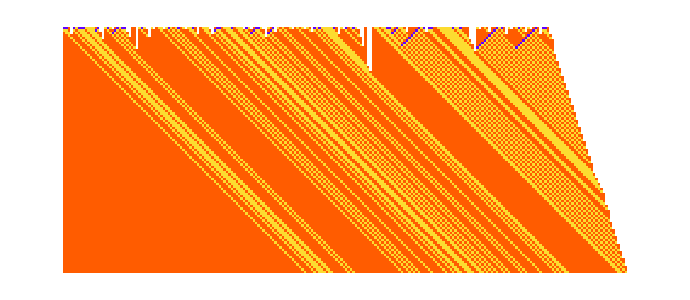

```mathematica
ArrayPlot[CellularAutomaton[{340282028880983993981473709559457473792, 4, 1}, {RandomChoice[{0,1, 2, 3}, 200], 0}, 100], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

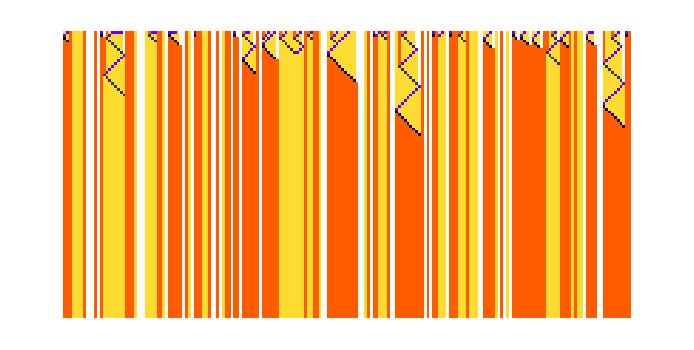

```mathematica
ArrayPlot[CellularAutomaton[{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, {RandomChoice[{0,1, 2, 3}, 200], 0}, 100], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

```mathematica
GraphicsGrid[Partition[Labeled[ArrayPlot[CellularAutomaton[<|"RuleNumber"->#,"Colors"->3|>,{{1,1,1,1,1,1,1,1,1,1,2},0},{{0,120},{-5,25}}],ColorRules-><|0->White,1->Black,2->GrayLevel[0.5]|>],Text[Style[#,Italic,7.5]],ImageSize->100]&/@{1920106431,5407067979,50663695617,50749793433,144892613592,238949703351,272425762404,272684219877,493427573370,837428508144,1380347975457,3385253974896,4510289298924,5616661823460,5616790963623,5794444905633,6424448193765,6463950373854,6463950380415,6863658437061,6863658437061,6937134280020,7050911966469,7066073564883},12],ImageSize->800]

GraphicsRow[Labeled[ArrayPlot[CellularAutomaton[<|"RuleNumber"->#,"Colors"->3|>,{Join[Table[1,60],{2}],0},{{0,400},{-5,125}}],ImageSize->150,ColorRules-><|0->White,1->Black,2->GrayLevel[0.5]|>],Text[Style[#,Italic]],ImageSize->160]&/@{144892613592,493427573370,837428508144,4510289298924,6424448193765,6463950373854},ImageSize->1050]
```

```mathematica
CellularAutomaton[]
```

```mathematica
Column[GraphicsRow[Table[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{#, 3, 1},{Join[Table[1,3],{2}],0},{40,{-5,10}}, 1], Mesh->True, "Trim"->{None, None}], 5]]&/@ {1920106431,5407067979,50663695617,50749793433,144892613592,238949703351,272425762404,272684219877,493427573370,837428508144,1380347975457,3385253974896,4510289298924,5616661823460,5616790963623,5794444905633,6424448193765,6463950373854,6463950380415,6863658437061,6863658437061,6937134280020,7050911966469,7066073564883}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[Function[rule, GraphicsRow[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{rule, 3, 1},{Join[Table[1,10],{2}],0},{30,{-5,50}}, #], Mesh->False, "Trim"->{None, None}]&/@ Prepend[Table[1, 5], <||>]]]/@ {144892613592,493427573370,837428508144,4510289298924,6424448193765,6463950373854}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[Function[rule, GraphicsRow[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{rule, 3, 1},{Join[Table[1,4],{2}],0},{30,{-5,30}}, #], Mesh->False, "Trim"->{None, None}]&/@ Prepend[Table[1, 5], <||>]]]/@ {1920106431,5407067979,50663695617,50749793433,144892613592,238949703351,272425762404,272684219877,493427573370,837428508144,1380347975457,3385253974896,4510289298924,5616661823460,5616790963623,5794444905633,6424448193765,6463950373854,6463950380415,6863658437061,6863658437061,6937134280020,7050911966469,7066073564883}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

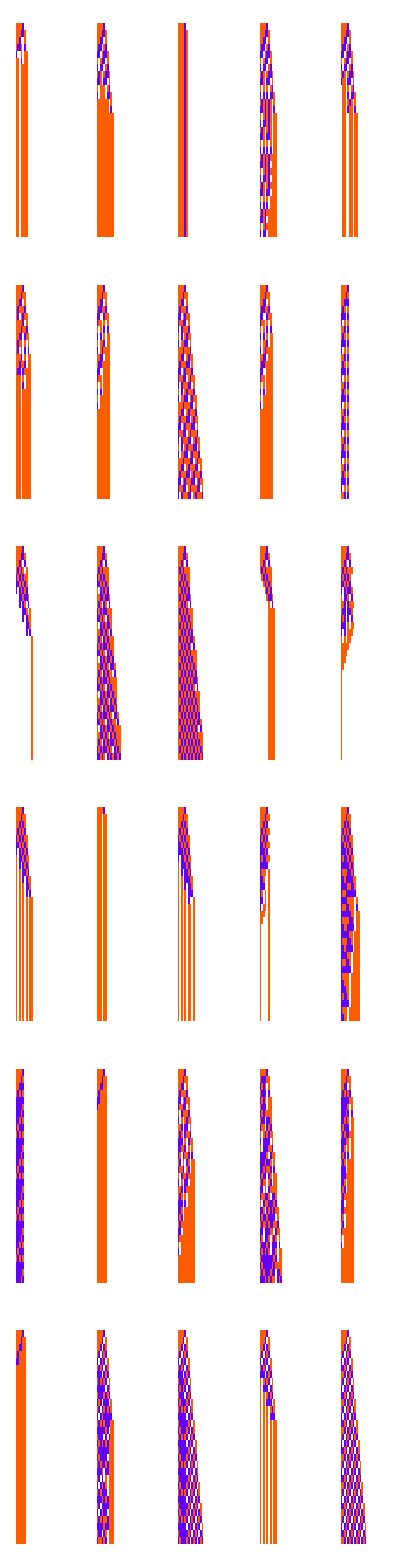

```mathematica
Column[Function[rule, GraphicsRow[Table[ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{rule, 3, 1}],{Join[Table[1,4],{2}],0},{30,{-5,30}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 5]]]/@ {144892613592,493427573370,837428508144,4510289298924,6424448193765,6463950373854}]
```

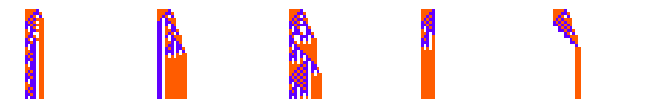

```mathematica
Column[Function[rule, GraphicsRow[Table[ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{rule, 3, 1}],{Join[Table[1,4],{2}],0},{30,{-5,30}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 5]]]/@ {1920106431,5407067979,50663695617,50749793433,144892613592,238949703351,272425762404,272684219877,493427573370,837428508144,1380347975457,3385253974896,4510289298924,5616661823460,5616790963623,5794444905633,6424448193765,6463950373854,6463950380415,6863658437061,6863658437061,6937134280020,7050911966469,7066073564883}[[{10}]]]
```

```mathematica
GraphicsGrid[Partition[Labeled[ArrayPlot[CellularAutomaton[<|"RuleNumber"->#,"Colors"->3|>,{{1,1,1,1,1,1,1,1,1,1,2},0},{{0,120},{-5,25}}],ColorRules-><|0->White,1->Black,2->GrayLevel[0.5]|>],Text[Style[#,Italic,7.5]],ImageSize->100]&/@{1920106431,5407067979,50663695617,50749793433,144892613592,238949703351,272425762404,272684219877,493427573370,837428508144,1380347975457,3385253974896,4510289298924,5616661823460,5616790963623,5794444905633,6424448193765,6463950373854,6463950380415,6863658437061,6863658437061,6937134280020,7050911966469,7066073564883},12],ImageSize->800]
```

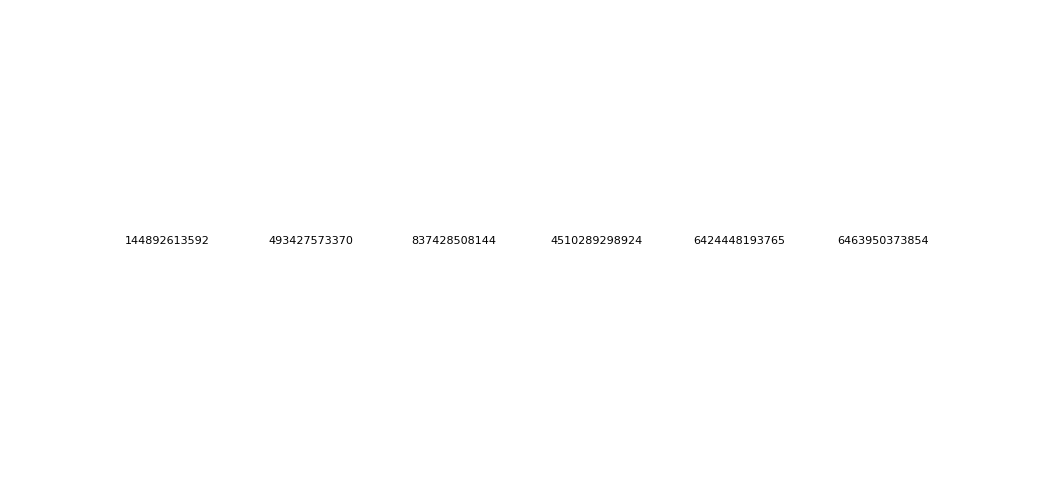

```mathematica
GraphicsRow[Labeled[ArrayPlot[CellularAutomaton[<|"RuleNumber"->#,"Colors"->3|>,{Join[Table[1,60],{2}],0},{{0,400},{-5,125}}],ImageSize->150,ColorRules-><|0->White,1->Black,2->GrayLevel[0.5]|>],Text[Style[#,Italic]],ImageSize->160]&/@{144892613592,493427573370,837428508144,4510289298924,6424448193765,6463950373854},ImageSize->1050]
```

```mathematica
Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo]
]
```

### Sensitivity plot

```mathematica
{1920106431,5407067979,50663695617,50749793433,144892613592,238949703351,272425762404,272684219877,493427573370,837428508144,1380347975457,3385253974896,4510289298924,5616661823460,5616790963623,5794444905633,6424448193765,6463950373854,6463950380415,6863658437061,6863658437061,6937134280020,7050911966469,7066073564883}[[10]]
```

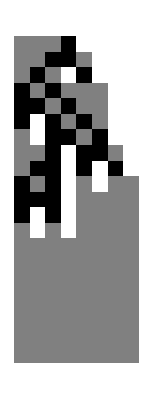

```mathematica
ArrayPlot[CellularAutomaton[{837428508144, 3, 1}, {Append[Table[1, 3], 2], 0}, 20]]
```

```mathematica
Column[Function[rule, GraphicsRow[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{rule, 3, 1},{Join[Table[1,10],{2}],0},{30,{-5,50}}, #], Mesh->False, "Trim"->{None, None}]&/@ Prepend[Table[1, 5], <||>]]]/@ {144892613592,493427573370,837428508144,4510289298924,6424448193765,6463950373854}]
```

```mathematica
lts=With[{aps=allperts[l1[[bmi[[1]],1]],{{1},0},{400,{-200,200}}]},ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]],1]],{{1},0},{400,{-200,200}},#]]&,aps]];
```

```mathematica
{144892613592,493427573370,837428508144,4510289298924,6424448193765,6463950373854}
```

```mathematica
rel = Abs[190  - #]&/@(lts/.-Infinity->401);
```

```mathematica
byidx = Partition[rel, 3];
```

```mathematica
blt = Mean/@byidx;
```

```mathematica
GraphicsRow[Reverse@{Module[{ca=CellularAutomaton[l1[[bmi[[1]],1]],{{1},0},200],lt},lt=TestCALifeTime[ca];
ArrayPlot[ReplacePart[Array[-1&,Dimensions[ca]],Thread[Catenate[bodyidxs[ca]]->blt]],ColorFunctionScaling->False,ColorFunction->(If[#==-1,White,Blend[{LightYellow,Yellow,Orange,Red},#/lt]]&)]],PlotCA[PerturbedCellularAutomaton[l1[[bmi[[1]],1]],{{1},0},{200,{-200,200}},{}],MeshStyle->Opacity[.1]]}]
```

```mathematica
CellularAutomaton[{837428508144, 3, 1}, {Append[Table[1, 3], 2], 0}, 20]
```

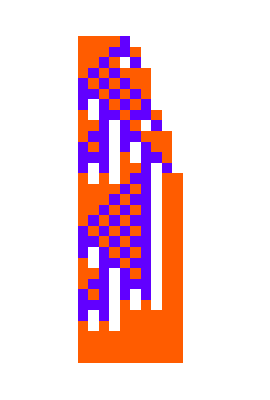
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,4],{2}],0},{30,{-5,15}}, #], Mesh->False, "Trim"->{None, None}, ImageSize->Tiny]&/@ Prepend[Table[1, 30], <||>]
```

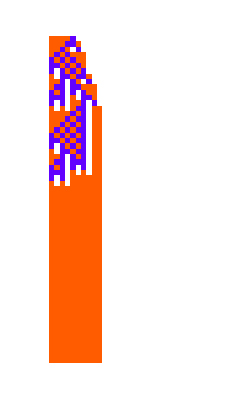
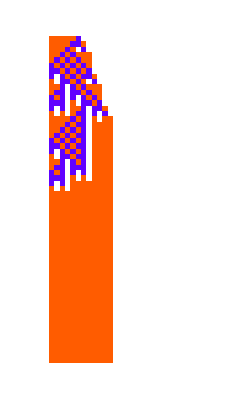
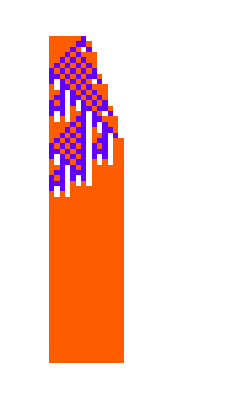
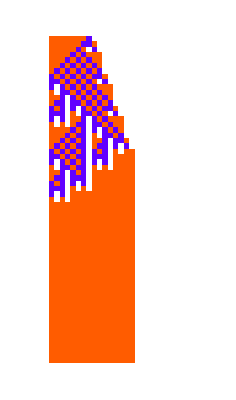
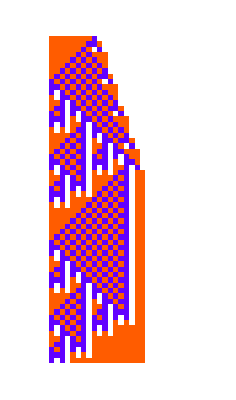
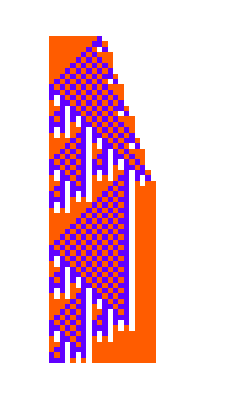
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,i],{2}],0},{60,{-5,30}}, #], Mesh->False, "Trim"->{None, None}, ImageSize->Tiny]&/@ Prepend[Table[1, 8], <||>], {i, 4, 10}]
```

```mathematica
Table[
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{837428508144, 3, 1},{Join[Table[1,4],{2}],0},{30,{-5,15}}, #], Mesh->False, "Trim"->{None, None}, ImageSize->Tiny]
]
```

```mathematica
With[{rule={{0,_,3}->0,{_,2,3}->3,{1,1,3}->4,{_,1,4}->4,{1|2,3,_}->5,{p:0|1,4,_}->7-p,{7,2,6}->3,{7,_,_}->7,{_,7,p:1|2}->p,{_,p:5|6,_}->7-p,{5|6,p:1|2,_}->7-p,{5|6,0,0}->1,{_,p:1|2,_}->p,{_,_,_}->0}},Labeled[GraphicsRow[MapIndexed[Labeled[ArrayPlot[CellularAutomaton[rule,{Append[Table[1,First[#2]+1],3],0},#1],Mesh->True,MeshStyle->GrayLevel[0.1],ColorRules-><|0->White,1->Black,_->Gray|>,ImageSize->{Automatic,300}],{Counts[Flatten[CellularAutomaton[rule,{Append[Table[1,First[#2]+1],3],0},{{First[#1][[2]]}}]]][1],First[#2]+1},{Bottom,Top}]&,{{{0,21},{-2,9}},{{0,37},{-3,16}},{{0,59},{-4,24}},{{0,87},{-5,35}}}],ImageSize->700],Text[Style[" input:"<>StringJoin[Table["\n",22]]<>"output:",Italic,GrayLevel[0.4],10]],Left]]
```

-Graphics- input:





















output:

```mathematica
With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0}},ArrayPlot[CellularAutomaton[rule,init,500],Epilog->{Inset[ArrayPlot[CellularAutomaton[rule,init,{{0,40},{-43,17}}],Mesh->True,MeshStyle->GrayLevel[0.3],ImageSize->270],Scaled[{0.24,0.81}]]},ImageSize->600]]
```

-Graphics-

```mathematica
With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0}},Show[ArrayPlot[CellularAutomaton[rule,init,{{0,40},{-43,17}}],Mesh->None,MeshStyle->GrayLevel[0.3],ImageSize->500], TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{Prime[i] + 2.5, Prime[i]}, {i, 1,12}], False, False, False}]]
```

-Graphics-

```mathematica
nonzeroRange[list_]:= SparseArray[list]["ExplicitPositions"] // If[Length[#] == 0, #, {#[[1, 1]], #[[-1, 1]]}]&
```

```mathematica
bodyidxs[ca_List]:= Block[{ranges =DeleteCases[nonzeroRange/@ ca, {}]},
Table[{i, #}&/@ Range@@ranges[[i]], {i, Length[ranges]}]
]
```

```mathematica
Module[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0},k = 16, r = 1,nperts = 10, ca, bis, vals},
ca = CellularAutomaton[rule,init,{{0,40},{-43,17}}];
bis = RandomChoice[Select[Catenate[bodyidxs[ca]], #[[1]]<20 &&#[[2]] > 45&], nperts]; 
vals = RandomChoice[Delete[Range[0, k - 1], ca[[#1, #2]]+1]]&@@@bis;
Show[{{"[◼]", "PlotCA"}}[{ReplacePart[ca, Thread[bis->vals]], AssociationThread[bis->vals]},ColorRules->Automatic,
 ColorFunction->(If[# == 0, White, Blend[{LightBlue, Blue}, #]]&)], TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{Prime[i] + .5, Prime[i]}, {i, 1,12}], False, False, False}]]
```

-Graphics-

```mathematica
Module[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0},k = 16, r = 1,nperts = 30, ca, bis, vals},
ca = CellularAutomaton[rule,init,100];
bis = RandomChoice[Select[Catenate[bodyidxs[ca]], #[[1]]<20 &&#[[2]] > 45&], nperts]; 
vals = RandomChoice[Delete[Range[0, k - 1], ca[[#1, #2]]+1]]&@@@bis;
(*vals = Table[0, nperts];*)
Show[{{"[◼]", "PlotCA"}}[{ReplacePart[ca, Thread[bis->vals]], AssociationThread[bis->vals]},ColorRules->Automatic,
 ColorFunction->(If[# == 0, White, Blend[{LightBlue, Blue}, #]]&), Mesh->None], TicksStyle->GrayLevel[.25],FrameTicksStyle->Directive[GrayLevel[.25], 10],FrameTicks->{Table[{Prime[i] - .5 , Prime[i]}, {i, 1,12}], False, False, False}]]
```

-Graphics-

```mathematica
Module[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0},k = 16, r = 1,nperts = 200, ca, bis, vals},
ca = CellularAutomaton[rule,init,{{75, 100}, Automatic}];
bis = RandomChoice[Select[Catenate[bodyidxs[ca]],(* #[[1]]<20 &&#[[2]] > 45&*)True&], nperts]; 
vals = RandomChoice[Delete[Range[0, k - 1], ca[[#1, #2]]+1]]&@@@bis;
vals = Table[-1, nperts];
Show[ArrayPlot[ReplacePart[ca, Thread[bis->vals]],ColorRules->-1->Red,
 ColorFunction->(If[# == 0, White,Blend[{LightBlue, Blue}, #]]&), Mesh->None], TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{Prime[i] - .5 , Prime[i]}, {i, 1,25}], False, False, False}]]
```

-Graphics-

```mathematica
Module[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0},k = 16, r = 1,nperts = 200, ca, bis, vals},
ca = CellularAutomaton[rule,init,{50, Automatic}];
bis = RandomChoice[Select[Catenate[bodyidxs[ca]],(* #[[1]]<20 &&#[[2]] > 45&*)True&], nperts]; 
vals = RandomChoice[Delete[Range[0, k - 1], ca[[#1, #2]]+1]]&@@@bis;
Show[ArrayPlot[ReplacePart[ca, Thread[bis->vals]],
 ColorFunction->(If[# == 0, White,Blend[{LightBlue, Blue}, #]]&), Mesh->None], TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{Prime[i] - .5 , Prime[i]}, {i, 1,15}], False, False, False}]]
```

-Graphics-

```mathematica
Table[{60*Prime[i] - 115, Prime[i]}, {i, 1,5}]
```

{{5,2},{65,3},{185,5},{305,7},{545,11}}

```mathematica
Association[{1->2}]
```

<|1→2|>

```mathematica
Show[{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{SparseArray[…],0},1600,Mesh->None,"Decay"->.99],TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{60*Prime[i] - 115, Prime[i]}, {i, 1,5}], False, False, False}]
```

```mathematica
SeedRandom[333333];
With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={RandomChoice[Range[0, 15], 30],0}},Show[ArrayPlot[CellularAutomaton[rule,init,{{0,40},{-43,40}}],Mesh->None,MeshStyle->GrayLevel[0.3],ImageSize->500], TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{Prime[i] + 2.5, Prime[i]}, {i, 1,12}], False, False, False}]]
```

-Graphics-

```mathematica
With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={MapAt[RandomChoice[Delete[Range[0, 15], # + 1]]&, {10, 0, 4, 8},RandomInteger[{1, 4}]] ,0}},Show[ArrayPlot[CellularAutomaton[rule,init,{{0,40},{-43,40}}],Mesh->None,MeshStyle->GrayLevel[0.3],ImageSize->500], TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{Prime[i] + 2.5, Prime[i]}, {i, 1,12}], False, False, False}]]
```

-Graphics-

```mathematica
Table[With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={MapAt[RandomChoice[Delete[Range[0, 15], # + 1]]&, {10, 0, 4, 8},RandomInteger[{1, 4}]] ,0}},ArrayPlot[CellularAutomaton[rule,init,{{0,100},Automatic}],Mesh->None, ImageSize->Tiny]], 30]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={RandomChoice[Range[0, 15], 30],0}},ArrayPlot[CellularAutomaton[rule,init,{{0,200},Automatic}],Mesh->None, ImageSize->Tiny, ColorFunction->(Blend[{White, Blue}, #]&)]], 100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Change the rule

```mathematica
Table[With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={MapAt[RandomChoice[Delete[Range[0, 15], # + 1]]&, {10, 0, 4, 8},RandomInteger[{1, 4}]] ,0}},ArrayPlot[CellularAutomaton[rule,init,{{0,40},Automatic}],Mesh->None, ImageSize->Tiny]], 30]
```